```mathematica
raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/results.json"];
raw = Association[#]&/@raw
```

{<|quad→Q5FF,axis→X,magnetConfigKey→upstream,PENT_xCenter→-0.0000139209,PENT_yCenter→-5.48706×10^-21|>,<|quad→Q5FF,axis→X,magnetConfigKey→PENT,PENT_xCenter→-0.0000185538,PENT_yCenter→1.28258×10^-19|>,<|quad→Q5FF,axis→X,magnetConfigKey→downstream,PENT_xCenter→-0.0000244145,PENT_yCenter→3.13013×10^-19|>,<|quad→Q5FF,axis→Y,magnetConfigKey→upstream,PENT_xCenter→-3.12452×10^-19,PENT_yCenter→-0.0000330706|>,<|quad→Q5FF,axis→Y,magnetConfigKey→PENT,PENT_xCenter→-8.99368×10^-18,PENT_yCenter→-0.0000235624|>,<|quad→Q5FF,axis→Y,magnetConfigKey→downstream,PENT_xCenter→-4.49244×10^-18,PENT_yCenter→-0.0000163432|>,<|quad→Q4FF,axis→X,magnetConfigKey→upstream,PENT_xCenter→-0.0000232119,PENT_yCenter→7.1713×10^-20|>,<|quad→Q4FF,axis→X,magnetConfigKey→PENT,PENT_xCenter→-0.0000282223,PENT_yCenter→-5.09219×10^-19|>,<|quad→Q4FF,axis→X,magnetConfigKey→downstream,PENT_xCenter→-0.000031697,PENT_yCenter→1.07456×10^-18|>,<|quad→Q4FF,axis→Y,magnetConfigKey→upstream,PENT_xCenter→6.45934×10^-18,PENT_yCenter→-0.0000138007|>,<|quad→Q4FF,axis→Y,magnetConfigKey→PENT,PENT_xCenter→7.88249×10^-18,PENT_yCenter→-8.714×10^-6|>,<|quad→Q4FF,axis→Y,magnetConfigKey→downstream,PENT_xCenter→-1.47787×10^-17,PENT_yCenter→-2.0083×10^-6|>,<|quad→Q3FF,axis→X,magnetConfigKey→upstream,PENT_xCenter→0.0000245327,PENT_yCenter→-8.48159×10^-21|>,<|quad→Q3FF,axis→X,magnetConfigKey→PENT,PENT_xCenter→0.0000278495,PENT_yCenter→-5.14266×10^-19|>,<|quad→Q3FF,axis→X,magnetConfigKey→downstream,PENT_xCenter→0.0000342826,PENT_yCenter→-8.57728×10^-19|>,<|quad→Q3FF,axis→Y,magnetConfigKey→upstream,PENT_xCenter→1.5241×10^-17,PENT_yCenter→5.2803×10^-6|>,<|quad→Q3FF,axis→Y,magnetConfigKey→PENT,PENT_xCenter→-5.48891×10^-18,PENT_yCenter→1.7106×10^-6|>,<|quad→Q3FF,axis→Y,magnetConfigKey→downstream,PENT_xCenter→-1.12688×10^-17,PENT_yCenter→-2.6909×10^-6|>,<|quad→Q2FF,axis→X,magnetConfigKey→upstream,PENT_xCenter→0.000126286,PENT_yCenter→-3.24215×10^-20|>,<|quad→Q2FF,axis→X,magnetConfigKey→PENT,PENT_xCenter→0.000126069,PENT_yCenter→-5.12584×10^-19|>,<|quad→Q2FF,axis→X,magnetConfigKey→downstream,PENT_xCenter→0.000112561,PENT_yCenter→-7.22356×10^-19|>,<|quad→Q2FF,axis→Y,magnetConfigKey→upstream,PENT_xCenter→-1.41526×10^-17,PENT_yCenter→-0.0000750962|>,<|quad→Q2FF,axis→Y,magnetConfigKey→PENT,PENT_xCenter→-1.56077×10^-18,PENT_yCenter→-0.000075054|>,<|quad→Q2FF,axis→Y,magnetConfigKey→downstream,PENT_xCenter→-1.18844×10^-17,PENT_yCenter→-0.0000752071|>,<|quad→Q1FF,axis→X,magnetConfigKey→upstream,PENT_xCenter→-0.000108738,PENT_yCenter→-1.40038×10^-19|>,<|quad→Q1FF,axis→X,magnetConfigKey→PENT,PENT_xCenter→-0.000108539,PENT_yCenter→-3.51867×10^-20|>,<|quad→Q1FF,axis→X,magnetConfigKey→downstream,PENT_xCenter→-0.00010329,PENT_yCenter→1.77311×10^-19|>,<|quad→Q1FF,axis→Y,magnetConfigKey→upstream,PENT_xCenter→-1.1565×10^-17,PENT_yCenter→0.000216762|>,<|quad→Q1FF,axis→Y,magnetConfigKey→PENT,PENT_xCenter→-2.73434×10^-18,PENT_yCenter→0.000212485|>,<|quad→Q1FF,axis→Y,magnetConfigKey→downstream,PENT_xCenter→1.57308×10^-17,PENT_yCenter→0.000214856|>,<|quad→Q0FF,axis→X,magnetConfigKey→upstream,PENT_xCenter→0.0000568264,PENT_yCenter→-1.29148×10^-19|>,<|quad→Q0FF,axis→X,magnetConfigKey→PENT,PENT_xCenter→0.0000556316,PENT_yCenter→-4.43226×10^-19|>,<|quad→Q0FF,axis→X,magnetConfigKey→downstream,PENT_xCenter→0.0000590547,PENT_yCenter→7.67833×10^-19|>,<|quad→Q0FF,axis→Y,magnetConfigKey→upstream,PENT_xCenter→4.28519×10^-17,PENT_yCenter→-0.0000621992|>,<|quad→Q0FF,axis→Y,magnetConfigKey→PENT,PENT_xCenter→1.65634×10^-18,PENT_yCenter→-0.0000607704|>,<|quad→Q0FF,axis→Y,magnetConfigKey→downstream,PENT_xCenter→-7.71427×10^-19,PENT_yCenter→-0.0000648792|>}

```mathematica
activeData = Select[raw,#quad == "Q5FF" && #axis =="X"&];
```

```mathematica
plotFunc[data_,label_]:=(
ListPlot[{#}&/@data,PlotRange->{{-200,200},{-200,200}},AspectRatio->1,ImageSize->800,LabelStyle->20,PlotLabel->label]
)
```

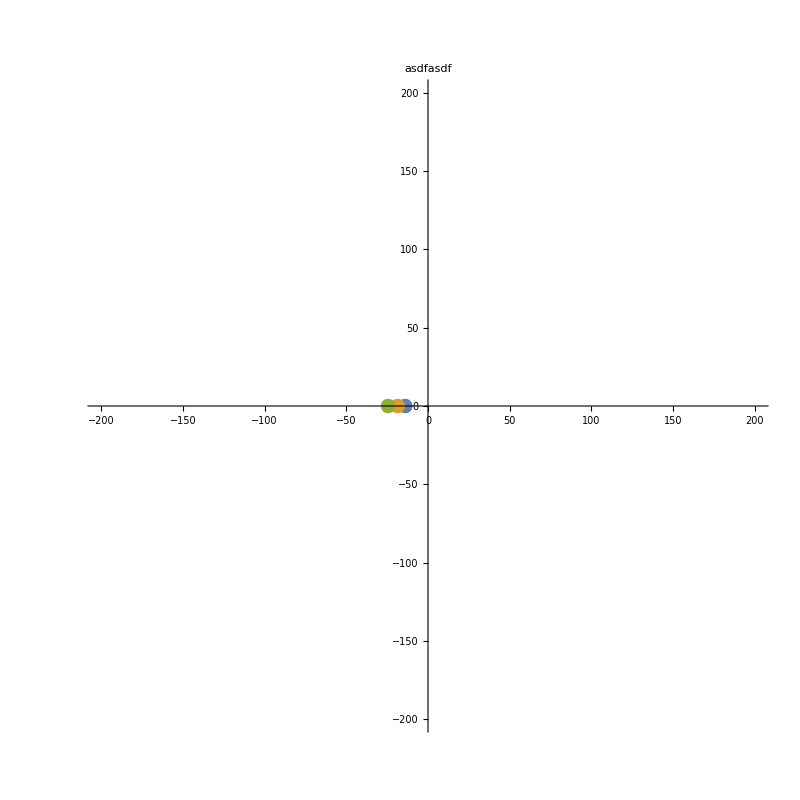

```mathematica
plotFunc[
10^6{#["PENT_xCenter"],#["PENT_yCenter"]}&/@activeData,
"asdfasdf"
]
```

```mathematica
DeleteDuplicates[raw[[All,"quad"]]]
```

{Q5FF,Q4FF,Q3FF,Q2FF,Q1FF,Q0FF}

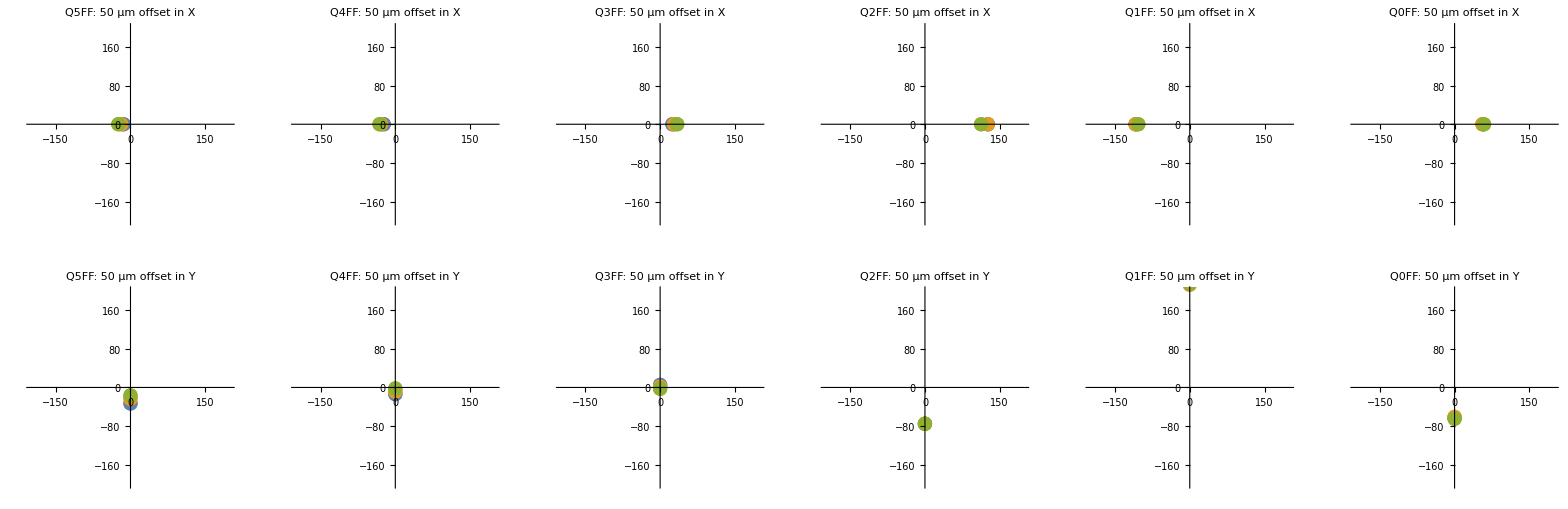

```mathematica
imgArr = Table[
activeData = Select[raw,#quad == quad && #axis ==axis&];

plotFunc[
10^6{#["PENT_xCenter"],#["PENT_yCenter"]}&/@activeData,
quad<>": 50 μm offset in "<>axis
],
{axis,{"X","Y"}},
{quad,DeleteDuplicates[raw[[All,"quad"]]]}


];
GraphicsGrid[imgArr,
ImageSize->3200]
```

```mathematica
tmpData = Table[
activeData = Select[raw,#quad == quad && #axis ==axis&];

{
quad,
axis,
10^6(activeData[[1,"PENT_xCenter"]] - activeData[[3,"PENT_xCenter"]]),
10^6(activeData[[1,"PENT_yCenter"]] - activeData[[3,"PENT_yCenter"]])
},

{quad,DeleteDuplicates[raw[[All,"quad"]]]},
{axis,{"X","Y"}}



]
```

{{{Q5FF,X,10.4936,-3.185×10^-13},{Q5FF,Y,4.17999×10^-12,-16.7274}},{{Q4FF,X,8.4851,-1.00285×10^-12},{Q4FF,Y,2.12381×10^-11,-11.7924}},{{Q3FF,X,-9.7499,8.49247×10^-13},{Q3FF,Y,2.65098×10^-11,7.9712}},{{Q2FF,X,13.7253,6.89934×10^-13},{Q2FF,Y,-2.26823×10^-12,0.1109}},{{Q1FF,X,-5.4482,-3.1735×10^-13},{Q1FF,Y,-2.72958×10^-11,1.9052}},{{Q0FF,X,-2.2283,-8.96981×10^-13},{Q0FF,Y,4.36233×10^-11,2.68}}}

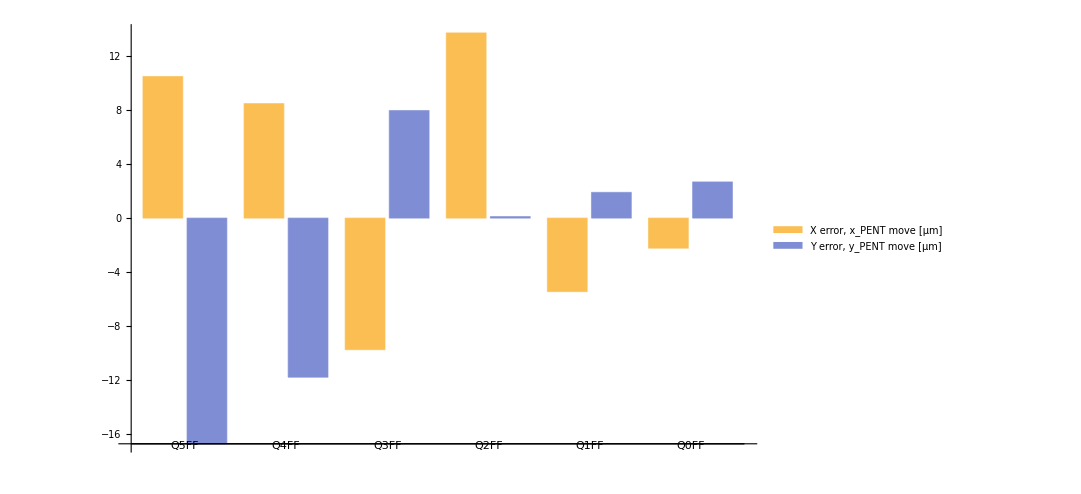

```mathematica
BarChart[Transpose[{
tmpData[[All,All,3]][[All,1]],
tmpData[[All,All,4]][[All,2]]
}],
ImageSize->800,
ChartLegends->Placed[{"X error, x_PENT move [μm]","Y error, y_PENT move [μm]"},{0.2,0.9}],
LabelStyle->20,
ChartLabels->{{"Q5FF","Q4FF","Q3FF","Q2FF","Q1FF","Q0FF"},None}
]
```

```mathematica
Table[
activeData = Select[raw,#quad == quad && #axis ==axis&];



Print["50 μm ", quad," error in ",axis, " moves x_PENT by ", Round[10^6(activeData[[1,"PENT_xCenter"]] - activeData[[3,"PENT_xCenter"]]),0.1], " μm and y_PENT by ",Round[10^6(activeData[[1,"PENT_yCenter"]] - activeData[[3,"PENT_yCenter"]]),0.1], " μm"],
{quad,DeleteDuplicates[raw[[All,"quad"]]]},
{axis,{"X","Y"}}



];
```

50 μm Q5FF error in X moves x_PENT by 10.5 μm and y_PENT by 0. μm

50 μm Q5FF error in Y moves x_PENT by 0. μm and y_PENT by -16.7 μm

50 μm Q4FF error in X moves x_PENT by 8.5 μm and y_PENT by 0. μm

50 μm Q4FF error in Y moves x_PENT by 0. μm and y_PENT by -11.8 μm

50 μm Q3FF error in X moves x_PENT by -9.7 μm and y_PENT by 0. μm

50 μm Q3FF error in Y moves x_PENT by 0. μm and y_PENT by 8. μm

50 μm Q2FF error in X moves x_PENT by 13.7 μm and y_PENT by 0. μm

50 μm Q2FF error in Y moves x_PENT by 0. μm and y_PENT by 0.1 μm

50 μm Q1FF error in X moves x_PENT by -5.4 μm and y_PENT by 0. μm

50 μm Q1FF error in Y moves x_PENT by 0. μm and y_PENT by 1.9 μm

50 μm Q0FF error in X moves x_PENT by -2.2 μm and y_PENT by 0. μm

50 μm Q0FF error in Y moves x_PENT by 0. μm and y_PENT by 2.7 μm

```mathematica
Table[
activeData = Select[raw,#quad == quad && #axis ==axis&];

centroidMoveμm = Norm[{Round[10^6(activeData[[1,"PENT_xCenter"]] - activeData[[3,"PENT_xCenter"]]),0.1],Round[10^6(activeData[[1,"PENT_yCenter"]] - activeData[[3,"PENT_yCenter"]]),0.1]}];

Print["Max allowed ", quad," error in ",axis, " (for 50 μm centroid shift) is ",50*50/centroidMoveμm, " μm"];

Nothing,
{quad,DeleteDuplicates[raw[[All,"quad"]]]},
{axis,{"X","Y"}}



];
```

Max allowed Q5FF error in X (for 50 μm centroid shift) is 238.095 μm

Max allowed Q5FF error in Y (for 50 μm centroid shift) is 149.701 μm

Max allowed Q4FF error in X (for 50 μm centroid shift) is 294.118 μm

Max allowed Q4FF error in Y (for 50 μm centroid shift) is 211.864 μm

Max allowed Q3FF error in X (for 50 μm centroid shift) is 257.732 μm

Max allowed Q3FF error in Y (for 50 μm centroid shift) is 312.5 μm

Max allowed Q2FF error in X (for 50 μm centroid shift) is 182.482 μm

Max allowed Q2FF error in Y (for 50 μm centroid shift) is 25000. μm

Max allowed Q1FF error in X (for 50 μm centroid shift) is 462.963 μm

Max allowed Q1FF error in Y (for 50 μm centroid shift) is 1315.79 μm

Max allowed Q0FF error in X (for 50 μm centroid shift) is 1136.36 μm

Max allowed Q0FF error in Y (for 50 μm centroid shift) is 925.926 μm